```mathematica
SetDirectory[NotebookDirectory[]];
```

# A workbook for B-set 3

## 4. Slash Guitar

```mathematica
slash=Import["files/guitar_stairwell.mat","Data"];
```

### Extract .mat file into variables

```mathematica
Fs=IntegerPart@slash[[1]][[1]][[1]];
h$stairwell=Flatten@Transpose@slash[[2]];
x=Flatten@Transpose@slash[[3]];
```

### Play guitar sound

```mathematica
ListPlay[x,SampleRate->Fs]
```

-Graphics-

### Play stairwell snap

```mathematica
ListPlay[h$stairwell,SampleRate->Fs]
```

-Graphics-

### Convolution with maximal overhang and zero padding

```mathematica
ListPlay[ListConvolve[h$stairwell,x,{1,-1},0],SampleRate->Fs]
```

-Graphics-

## 5.

```mathematica
FFTShift[data_]:=Module[{},RotateRight[Fourier[data],Floor@(Length[data]/2)]]
```

```mathematica
handel=Flatten@Transpose@Import["files/handel.csv","Data"];
FsHandel=8192;
```

### 1 % make a vector for the time indices 2 % technically, this is supposed to go from 3 % - infinity to +infinity, but this will be long enough 4 n = [-42:41]; 5 % generate a sinc function corresponding to 6 % a LPF with cutoff frequency of wc 7 h = wc/pi*sinc(wc*n/pi);

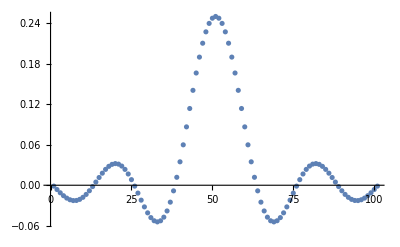

```mathematica
n=Range[-50,50];
wc=Pi/4;
h$lowpass=wc/Pi Sinc[(wc*n)/Pi];
ListPlot[h$lowpass]
```

```mathematica
handelLowpassed=ListConvolve[h$lowpass,handel]
```

{0.235931,0.230184,0.216683,0.196649,0.171376,0.142514,0.111416,0.0793651,0.0479663,0.018912,-0.00611131,-0.0254358,72990,-0.110133,-0.0897076,-0.0705895,-0.0543485,-0.0417717,-0.0340142,-0.0316567,-0.0341177,-0.0408176,-0.0509422,-0.0629706}
 |  |  |  |

```mathematica
ListPlay[handelLowpassed,SampleRate->FsHandel]
```

-Graphics-

```mathematica
ListPlay[handel,SampleRate->FsHandel]
```

-Graphics-

```mathematica
handelPlot=ListLinePlot[handel,PlotRange->Full,ImageSize->Medium];
handelLowpassedPlot=ListLinePlot[handelLowpassed,PlotRange->Full,ImageSize->Medium];
```

```mathematica
handelFourierPlot=ListLinePlot[Abs@FFTShift[handel],PlotRange->Full,ImageSize->Medium];
handelFourierLowpassedPlot=ListLinePlot[Abs@FFTShift[handelLowpassed],PlotRange->Full,ImageSize->Medium];
```

```mathematica
Rasterize@Grid[Transpose@{{"Handel original","Handel lowpassed","Handel original fft","Handel lowpassed fft"},{handelPlot,handelLowpassedPlot,handelFourierPlot,handelFourierLowpassedPlot}}]
```

-Graphics-

### Plot of original vs lowpassed fft. For some reason, my lowpass doesn’t seem to be lowpassing correctly. As can be seen by the shifted positions of the spikes in the center. That being said, it sounds exactly like it should.

```mathematica
Rasterize@ListLinePlot[{Abs@FFTShift[handel],Abs@FFTShift[handelLowpassed]},PlotRange->Full]
```

-Graphics-

## 5. b

```mathematica
Length[handel]
Length[handelLowpassed]
```

73113

73013

```mathematica
Length[FFTShift[handel][[51;;Length[handel]-50]]]
Length[FFTShift[handelLowpassed]]
```

73013

73013

```mathematica
FFTShift[handel][[1]]
```

0.00913144+0.0053592 ⅈ

```mathematica
FFTShift[handelLowpassed][[1]]
```

0.000576847+6.3852×10^-6 ⅈ

```mathematica
ListLinePlot[FFTShift[handel][[51;;Length[handel]-50]]-FFTShift[handelLowpassed],PlotRange->Full]
```

-Graphics-

## 6. c

```mathematica
Fs$6=Import["files/TwoAM.wav","SampleRate"]
twoAMData=Import["files/TwoAM.wav","Data"]
```

44100

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,217035,-0.00408936,-0.000305176,0.00311289,0.00216681,-0.000305176,-0.000305176,0.000640889,-0.00109863,-0.003479,-0.0015564,0.00305185,0.00390637,0.000335704,-0.00210571,-0.0012207,0.0000915555,0.000122074,-0.0000610352,0.0000915555,0.000152593}
 |  |  |  |

### Plot of the fftshift of twoAMData

```mathematica
Rasterize@ListLinePlot[Transpose@{Subdivide[N@-Pi/2,Pi/2,Length[twoAMData]-1],Abs@FFTShift[twoAMData]},ImageSize->Large,PlotRange->Full]
```

-Graphics-

### Just notes on how to scale the plot with proper lengths. Subdivide needs a -1 to be the same length as the original data.

```mathematica
Length@Subdivide[N@-Pi/2,Pi/2,Length[twoAMData]-1]
Length@Abs@FFTShift[twoAMData]
```

217075

217075

### Try to extract sounds by multiplying by cos

```mathematica
Ωx=(16000/Fs$6)π;
Ωw=(6000/Fs$6)π;
ΩM=0.3;
```

### In the case of shifting, we use MapIndex to refer to the position of the item in the list.

```mathematica
xshifted=Flatten@Transpose@MapIndexed[Cos[Ωx*#2]*#1&,twoAMData];
wshifted=Flatten@Transpose@MapIndexed[Cos[Ωw*#2]*#1&,twoAMData];
```

### First reconstruct the violin

```mathematica
Rasterize@ListLinePlot[Transpose@{Subdivide[N@-Pi/2,Pi/2,Length[xshifted]-1],Abs@FFTShift[xshifted]},ImageSize->Large,PlotRange->Full]
```

-Graphics-

### Bandpass is done on the DT shifted signal. Not on the fft.

```mathematica
xbandpassed=BandpassFilter[xshifted,{0,.15Pi}]
Rasterize@ListLinePlot[Transpose@{Subdivide[N@-Pi/2,Pi/2,Length[xbandpassed]-1],Abs@FFTShift[xbandpassed]},ImageSize->Large,PlotRange->Full]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-8.29123×10^-8,-1.23143×10^-7,217021,0.000410441,0.000152721,-0.000100416,-0.000321499,-0.000506476,-0.000649975,-0.000713902,-0.000736793,-0.000693121,-0.000580867,-0.000434344,-0.000242053,-0.0000297855,0.000184965,0.00037812,0.000533239,0.000640904,0.000677619,0.000660052,0.000593056,0.000483161,0.000363684,0.000243276,0.000137874,0.0000542817,-1.49404×10^-6,-0.0000347525}
 |  |  |  |

-Graphics-

### Successfully recreated violin sound

```mathematica
ListPlay[xbandpassed,SampleRate->Fs$6]
```

-Graphics-

### Next reconstruct the guitar

```mathematica
wbandpassed=BandpassFilter[wshifted,{0,.15Pi}]
Rasterize@ListLinePlot[Transpose@{Subdivide[N@-Pi/2,Pi/2,Length[wbandpassed]-1],Abs@FFTShift[wbandpassed]},ImageSize->Large,PlotRange->Full]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,217039,0.000631935,0.000626164,0.0005171,0.000319317,0.0000684776,-0.000197523,-0.000438912,-0.000606631,-0.000669361,-0.000628711,-0.000501768,-0.000317751,-0.000126172,0.0000265447,0.000122111,0.000161779,0.000159534,0.000144692}
 |  |  |  |

-Graphics-

```mathematica
wbandpassed=BandpassFilter[wshifted,{0,.15Pi}]
Rasterize@ListLinePlot[Transpose@{Subdivide[N@-Pi/2,Pi/2,Length[wbandpassed]-1],Abs@FFTShift[wbandpassed]},ImageSize->Large,PlotRange->Full]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,217039,0.000631935,0.000626164,0.0005171,0.000319317,0.0000684776,-0.000197523,-0.000438912,-0.000606631,-0.000669361,-0.000628711,-0.000501768,-0.000317751,-0.000126172,0.0000265447,0.000122111,0.000161779,0.000159534,0.000144692}
 |  |  |  |

-Graphics-

### Successfully recreated guitar sound

```mathematica
ListPlay[wbandpassed,SampleRate->Fs$6]
```

-Graphics-